```mathematica
CoefficientList[Series[(x+1)^(1/15),{x,0,16}],x]
```

{1,1/15,-7/225,203/10125,-2233/151875,131747/11390625,-4874639/512578125,61977553/7688671875,-805708189/115330078125,95879274491/15569560546875,-6423911390897/1167717041015625,87014799749423/17515755615234375,-3567606789726343/788209002685546875,49123201181616569/11823135040283203125,-680707216373829599/177347025604248046875,142267808222130386191/39903080760955810546875,-1991749315109825406674/598546211414337158203125}

```mathematica
CoefficientList[Series[(x+1)^(-1/15),{x,0,16}],x]
```

{1,-1/15,8/225,-248/10125,2852/151875,-173972/11390625,6610936/512578125,-85942168/7688671875,1138733726/115330078125,-137786780846/15569560546875,9369501097528/1167717041015625,-128617696884248/17515755615234375,5337634420696292/788209002685546875,-74316294626617604/11823135040283203125,1040428124772646456/177347025604248046875,-219530334327028402216/39903080760955810546875,3100865972369276181301/598546211414337158203125}

```mathematica
CoefficientList[Series[(x+1)^(-1/2),{x,0,16}],x]
```

{1,-1/2,3/8,-5/16,35/128,-63/256,231/1024,-429/2048,6435/32768,-12155/65536,46189/262144,-88179/524288,676039/4194304,-1300075/8388608,5014575/33554432,-9694845/67108864,300540195/2147483648}

```mathematica
CoefficientList[Series[(x+1)^(1/2),{x,0,16}],x]
```

{1,1/2,-1/8,1/16,-5/128,7/256,-21/1024,33/2048,-429/32768,715/65536,-2431/262144,4199/524288,-29393/4194304,52003/8388608,-185725/33554432,334305/67108864,-9694845/2147483648}

```mathematica
co := CoefficientList[Series[(x+1)^a,{x,0,16}],x]
```

```mathematica
Table[ co[[n]],{n,0,16}]//TableForm
```

List
1
a
1/2 (-1+a) a
1/6 (-2+a) (-1+a) a
1/24 (-3+a) (-2+a) (-1+a) a
1/120 (-4+a) (-3+a) (-2+a) (-1+a) a
1/720 (-5+a) (-4+a) (-3+a) (-2+a) (-1+a) a
((-6+a) (-5+a) (-4+a) (-3+a) (-2+a) (-1+a) a)/5040
((-7+a) (-6+a) (-5+a) (-4+a) (-3+a) (-2+a) (-1+a) a)/40320
((-8+a) (-7+a) (-6+a) (-5+a) (-4+a) (-3+a) (-2+a) (-1+a) a)/362880
((-9+a) (-8+a) (-7+a) (-6+a) (-5+a) (-4+a) (-3+a) (-2+a) (-1+a) a)/3628800
((-10+a) (-9+a) (-8+a) (-7+a) (-6+a) (-5+a) (-4+a) (-3+a) (-2+a) (-1+a) a)/39916800
((-11+a) (-10+a) (-9+a) (-8+a) (-7+a) (-6+a) (-5+a) (-4+a) (-3+a) (-2+a) (-1+a) a)/479001600
((-12+a) (-11+a) (-10+a) (-9+a) (-8+a) (-7+a) (-6+a) (-5+a) (-4+a) (-3+a) (-2+a) (-1+a) a)/6227020800
((-13+a) (-12+a) (-11+a) (-10+a) (-9+a) (-8+a) (-7+a) (-6+a) (-5+a) (-4+a) (-3+a) (-2+a) (-1+a) a)/87178291200
((-14+a) (-13+a) (-12+a) (-11+a) (-10+a) (-9+a) (-8+a) (-7+a) (-6+a) (-5+a) (-4+a) (-3+a) (-2+a) (-1+a) a)/1307674368000

```mathematica
Pochhammer[a-4,5]/5!
```

1/120 (-4+a) (-3+a) (-2+a) (-1+a) a

```mathematica
5!
```

120

```mathematica
Gamma[6]
```

120

```mathematica
Pw[x_, a_, t_] := Sum[ Gamma[a+1]/(Gamma[a-k+1] Gamma[k+1] ) (x-1)^k,{k,0,t}]
```

```mathematica
Pw[1.03,.7,220]
```

1.02091

```mathematica
1.03^.7
```

1.02091

```mathematica
D2[n_,k_]:=Sum[D2[Floor[n/j],k-1],{j,2,n}];D2[n_,0]:=1
d[n_,z_]:=Product[Pochhammer[z,a=p[[2]]]/a!,{p,FI[n]}];FI[n_]:=FactorInteger[n];FI[1]:={}
DD[n_,k_]:=Sum[d[j,k],{j,1,n}]
```

```mathematica
DD[100,3.7]
```

2787.64

```mathematica
DD[100,-3.3]
```

62.6314

```mathematica
DD[100,2.2+3.2I]
```

-2014.18+106.902 ⅈ

```mathematica
Dw[x_, a_] := Sum[ Gamma[a+1]/(Gamma[a-k+1] Gamma[k+1] ) D2[x,k],{k,0,Log[2,x]}]
```

```mathematica
Dw[100,3.7]
```

2787.64

```mathematica
Dw[100,-3.3]
```

62.6314

```mathematica
Dw[500,-1.00000000001]
```

-6.01483

```mathematica
22.007322536523986
```

```mathematica
DD[500,-1]
```

-6

```mathematica
D2[100,3]
```

324

```mathematica
Dw2[x_, a_,t_] := Sum[(-1)^(a-k) Gamma[a+1]/(Gamma[a-k+1] Gamma[k+1] ) DD[x,k],{k,0,t}]
```

```mathematica
Dw2[100,2.2,60]
```

-11620.1-8442.5 ⅈ

```mathematica
CoefficientList[Series[(x+1)^a,{x,0,16}],x]
```

{1,2,1}

```mathematica
CoefficientList[Series[(x-1)^b,{x,0,16}],x]
```

{(-1)^b,-(-1)^b b,1/2 (-1)^b (-1+b) b,-1/6 (-1)^b (-2+b) (-1+b) b,1/24 (-1)^(-4+b) (-3+b) (-2+b) (-1+b) b,1/120 (-1)^(-5+b) (-4+b) (-3+b) (-2+b) (-1+b) b,1/720 (-1)^(-6+b) (-5+b) (-4+b) (-3+b) (-2+b) (-1+b) b,((-1)^(-7+b) (-6+b) (-5+b) (-4+b) (-3+b) (-2+b) (-1+b) b)/5040,((-1)^(-8+b) (-7+b) (-6+b) (-5+b) (-4+b) (-3+b) (-2+b) (-1+b) b)/40320,((-1)^(-9+b) (-8+b) (-7+b) (-6+b) (-5+b) (-4+b) (-3+b) (-2+b) (-1+b) b)/362880,((-1)^(-10+b) (-9+b) (-8+b) (-7+b) (-6+b) (-5+b) (-4+b) (-3+b) (-2+b) (-1+b) b)/3628800,((-1)^(-11+b) (-10+b) (-9+b) (-8+b) (-7+b) (-6+b) (-5+b) (-4+b) (-3+b) (-2+b) (-1+b) b)/39916800,1/479001600(-1)^(-12+b) (-11+b) (-10+b) (-9+b) (-8+b) (-7+b) (-6+b) (-5+b) (-4+b) (-3+b) (-2+b) (-1+b) b,1/6227020800(-1)^(-13+b) (-12+b) (-11+b) (-10+b) (-9+b) (-8+b) (-7+b) (-6+b) (-5+b) (-4+b) (-3+b) (-2+b) (-1+b) b,1/87178291200(-1)^(-14+b) (-13+b) (-12+b) (-11+b) (-10+b) (-9+b) (-8+b) (-7+b) (-6+b) (-5+b) (-4+b) (-3+b) (-2+b) (-1+b) b,1/1307674368000(-1)^(-15+b) (-14+b) (-13+b) (-12+b) (-11+b) (-10+b) (-9+b) (-8+b) (-7+b) (-6+b) (-5+b) (-4+b) (-3+b) (-2+b) (-1+b) b,1/20922789888000(-1)^(-16+b) (-15+b) (-14+b) (-13+b) (-12+b) (-11+b) (-10+b) (-9+b) (-8+b) (-7+b) (-6+b) (-5+b) (-4+b) (-3+b) (-2+b) (-1+b) b}

```mathematica
Pwm[x_, a_, t_] := Sum[ (-1)^(a-k)Gamma[a+1]/(Gamma[a-k+1] Gamma[k+1] ) x^k,{k,0,t}]
```

```mathematica
N[Pwm[4,1/3,30]]
```

-2.07759×10^15-3.59848×10^15 ⅈ

```mathematica
4^3.3
```

97.0059

```mathematica
Pw[4,3.3,40]
```

3.13237×10^12

```mathematica
CoefficientList[Series[(1/(x-1)-1),{x,0,16}],x]
```

{-2,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1}

```mathematica
CoefficientList[Series[(1/(x+1)-1),{x,0,16}],x]
```

{0,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1}

```mathematica
CoefficientList[Series[(1/(x+1)-1)^2,{x,0,16}],x]
```

{0,0,1,-2,3,-4,5,-6,7,-8,9,-10,11,-12,13,-14,15}

```mathematica
FullSimplify[CoefficientList[Series[(1/(x-1)+1)^b,{x,0,16}],x]]
```

{(-x)^b (1+b x+1/2 b (1+b) x^2+1/6 b (1+b) (2+b) x^3+1/24 b (1+b) (2+b) (3+b) x^4+1/120 b (1+b) (2+b) (3+b) (4+b) x^5+1/720 b (1+b) (2+b) (3+b) (4+b) (5+b) x^6+(b (1+b) (2+b) (3+b) (4+b) (5+b) (6+b) x^7)/5040+(b (1+b) (2+b) (3+b) (4+b) (5+b) (6+b) (7+b) x^8)/40320+(b (1+b) (2+b) (3+b) (4+b) (5+b) (6+b) (7+b) (8+b) x^9)/362880+(b (1+b) (2+b) (3+b) (4+b) (5+b) (6+b) (7+b) (8+b) (9+b) x^10)/3628800+(b (1+b) (2+b) (3+b) (4+b) (5+b) (6+b) (7+b) (8+b) (9+b) (10+b) x^11)/39916800+(b (1+b) (2+b) (3+b) (4+b) (5+b) (6+b) (7+b) (8+b) (9+b) (10+b) (11+b) x^12)/479001600+1/6227020800 b (1+b) (2+b) (3+b) (4+b) (5+b) (6+b) (7+b) (8+b) (9+b) (10+b) (11+b) (12+b) x^13+1/87178291200 b (1+b) (2+b) (3+b) (4+b) (5+b) (6+b) (7+b) (8+b) (9+b) (10+b) (11+b) (12+b) (13+b) x^14+1/1307674368000 b (1+b) (2+b) (3+b) (4+b) (5+b) (6+b) (7+b) (8+b) (9+b) (10+b) (11+b) (12+b) (13+b) (14+b) x^15+1/20922789888000 b (1+b) (2+b) (3+b) (4+b) (5+b) (6+b) (7+b) (8+b) (9+b) (10+b) (11+b) (12+b) (13+b) (14+b) (15+b) x^16+O[x]^17)}

```mathematica
ClearAll["Global`*"]
Dhyp[n_,k_,a_]:=Sum[Binomial[k,j] Dhyp[n/(m^(k-j)),j,m+1],{m,a,n^(1/k)},{j,0,k-1}]
Dhyp[n_,1,a_]:=Floor[n]-a+1;Dhyp[n_,0,a_]:=1
Dwh[x_, a_,s_] := Sum[ N[Gamma[a+1]/(Gamma[a-k+1] Gamma[k+1] ) Dhyp[Floor[x/(s^(a-k))],k,s+1]],{k,0,Log[s+1,x]}]
```

```mathematica
(Dwh[100,0.1,3])
```

259.031

```mathematica
Dhyp[1040,2,2]
DD[1040,.1]
```

5317

23.6184

```mathematica
ClearAll["Global`*"]
```

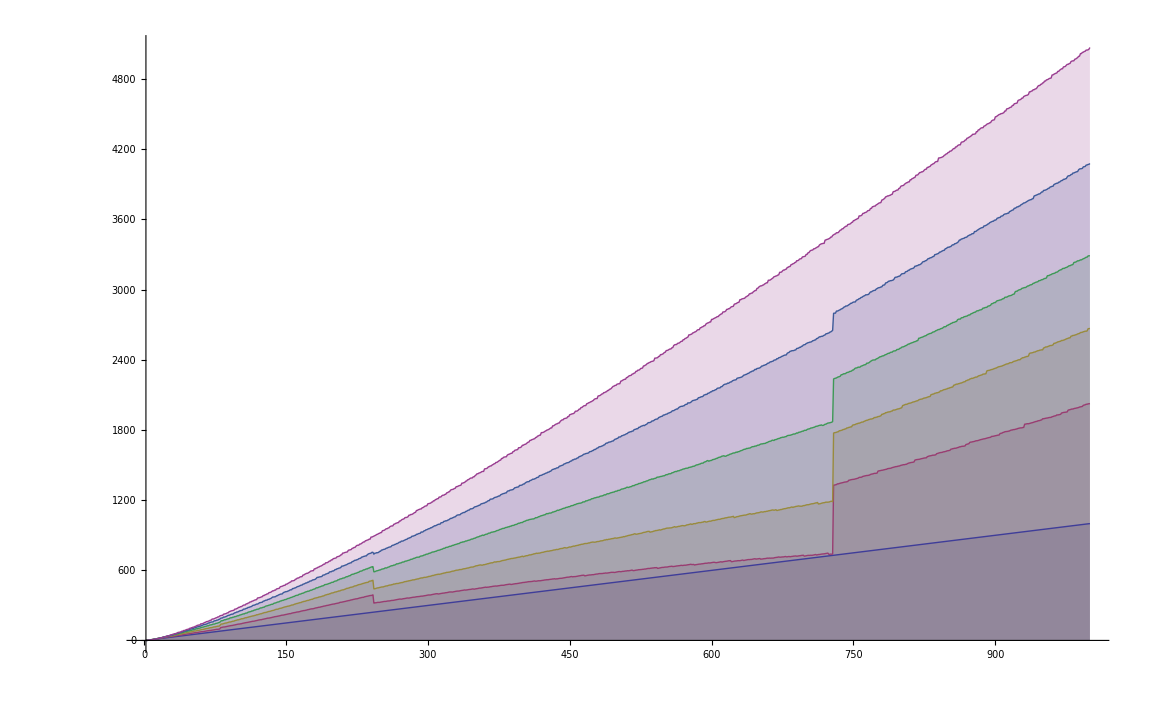

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$IterationLimit::itlim: Iteration limit of 4096 exceeded.

```mathematica
DiscretePlot[{ Dwh[n,1,2],Dwh[n,1+.2,2],Dwh[n,1+.4,2],Dwh[n,1+.6,2],Dwh[n,1+.8,2],Dwh[n,2,2]},{n,2,1000}]
```

```mathematica
f
```

$IterationLimit::itlim: Iteration limit of 4096 exceeded.

General::stop: Further output of $IterationLimit :: itlim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$Aborted

```mathematica
Dhyp[10000,4,3]
```

171994

```mathematica
Sum[Gamma[a+1]/(Gamma[a-k+1] Gamma[k+1]) (x-2)^k,{k,0,Infinity}]
```

(-1+x)^a

```mathematica
Sum[Gamma[3.3+1]/(Gamma[3.3-k+1] Gamma[k+1]) (x-2)^k,{k,0,Infinity}]
```

1. (-1.+x)^(33/10)